# Práctica 6: Juegos en Poblaciones Finitas

### Funciones:

```mathematica
GetColors[G_]:=Sort@Union[PropertyValue[{G,#},VertexStyle]&/@VertexList[G]]
```

```mathematica
Turno[G_,Payoff1_,Payoff2_,ω_,σ_]:=Module[{n=Length@VertexList[G],Poblaciones,temp,Fitness,keys,H=G},
	keys=GetColors@H;
	If[Length@keys==1,Return@H];
	Poblaciones=Count[Table[PropertyValue[{H,i},VertexStyle],{i,n}],#]&/@keys;
	Fitness=1-ω-σ+ω(Payoff1.Poblaciones-Diagonal[Payoff1])/(n-1)+σ(Payoff2.Poblaciones-Diagonal[Payoff2])/(n-1);
	PropertyValue[{H,RandomInteger[n]},VertexStyle]=RandomChoice[Fitness->keys];
	Return[H];
	]
```

```mathematica
Juego[G_,Payoff1_,Payoff2_,ω_,σ_,iter_]:=Module[{H,logs={},log={},score={},temp,n=VertexCount@G},
	Do[ log={};
		H=G;
		While[Length@GetColors@H>1,
			AppendTo[log,H];
			H=Turno[H,Payoff1,Payoff2,ω,σ];
			];
		temp=(First@Thread@GetPopulations@log)/n;
		If[Last@temp==1/n,AppendTo[temp,0],AppendTo[temp,1]];
		AppendTo[score,temp];
		log,iter];
	Return[score]
]
```

```mathematica
GetPopulation[G_]:=Module[{keys=GetColors[G],properties},
	properties=Table[PropertyValue[{G,i},VertexStyle],{i,VertexCount@G}];
	Return[Count[properties,#]&/@keys]
	]
```

```mathematica
GetPopulations[Glist_]:=Table[GetPopulation[g],{g,Glist}]
```

```mathematica
PromedioMuestral[G_,Payoff_,tamañoSimulacion_,numSimulacion_]:=Module[{Poblaciones=0},
	Do[Poblaciones+=GetPopulations[Juego[G,Payoff,tamañoSimulacion]];,numSimulacion];
	Poblaciones/numSimulacion
	]
```

## Experimento - La idea es dividir una matriz en una suma de matrices con equilibrios racionales. De esta manera se puede entender la matriz original como la suma de ponderada de varias decisiones racionales.

### A es ESSN para N > 12

```mathematica
A={{20,0},{17,1}} + 10; (*Ejemplo A*)
```

### La primera estrategia es racional en Payoff1 mientras que la segunda es racional en Payoff2

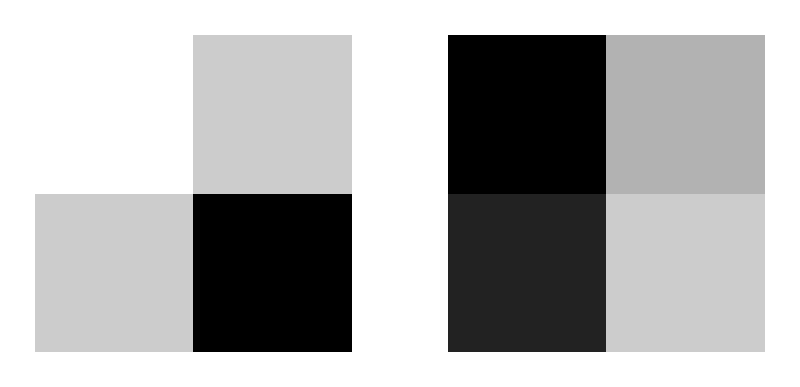

```mathematica
Payoff1={{0,1},{1,5}};(*Dilema del prisionero*)
Payoff2=A-Payoff1;
GraphicsRow[{ArrayPlot@Payoff1,ArrayPlot@Payoff2}]
```

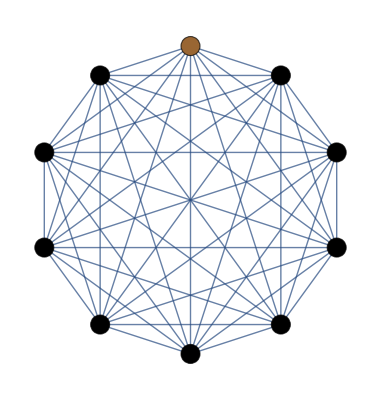

```mathematica
n=10;
G=CompleteGraph[n,VertexStyle->Thread[#-> If[#≠n,Black,Brown]&/@Range[n]],VertexSize->0.2]
```

```mathematica
Manipulate[
	score=Juego[G,Payoff1,Payoff2,ω,σ,20];
	lp=Show[ListPlot[score,PlotRange->{Full,{-0.1,1.1}},Joined->True,
			Axes->{False,True},GridLines->{None,{0,1}},GridLinesStyle->Directive[Gray, Dashed],
			Ticks->{None, {{0,"B"},{1,"A"}}}],
			ListPlot[Thread[{Length/@score,Last/@score}],PlotStyle->{PointSize[0.025],Black} ],
			ListPlot[Thread[{Length/@score,Last/@score}],PlotStyle->{PointSize[0.01],White} ] ,ImageSize->Large];
	pch = PieChart[ Table[ Count[Last/@score,i]/Length[score]//N,{i,0,1}] ,
			ChartLabels->Placed[{"B","A"},"RadialCallout"],LabelingFunction->"RadialCenter",ImageSize->Large];
	GraphicsRow[{lp,pch},ImageSize->{{1100,300},{400,400}}+200],
	{{ω,0.518},0,1},
	{σ,0,1}]
```